```mathematica
crosscheck[{{aa_,bb_},{cc_,dd_}}] :=
 If[Length[Union[{aa,bb,cc,dd}]]==3, True,
If[bb<cc || bb>dd,True,False]]
```

```mathematica
linechecker[zz_List] := If[Union[Map[crosscheck[#]&,Subsets[zz,{2}]]]=={True},True,False]
```

```mathematica
triangulations = Table[Last/@Select[Sort[Map[{linechecker[#],#}&,Sort/@Subsets[Sort[Drop[Flatten[Reverse[Table[{a,b},{a,1,sides-2},{b,a+2,sides}]],1],-1]],{sides-3}]]],First[#]==True&],{sides,5,8}];
```

```mathematica
gg=5;
```

```mathematica
pts=Table[N[{Cos[x],Sin[x]}],{x,2Pi/gg,2Pi,2Pi/gg}]
```

{{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057},{1.,0.}}

```mathematica
lines=triangulations[[gg-4]]
```

{{{1,3},{1,4}},{{1,3},{3,5}},{{1,4},{2,4}},{{2,4},{2,5}},{{2,5},{3,5}}}

```mathematica
Table[Map[pts[[#]]&,lines[[n]]],{n,1,Length[lines]}]
```

{{{{0.309017,0.951057},{-0.809017,-0.587785}},{{0.309017,0.951057},{0.309017,-0.951057}}},{{{0.309017,0.951057},{-0.809017,-0.587785}},{{-0.809017,-0.587785},{1.,0.}}},{{{0.309017,0.951057},{0.309017,-0.951057}},{{-0.809017,0.587785},{0.309017,-0.951057}}},{{{-0.809017,0.587785},{0.309017,-0.951057}},{{-0.809017,0.587785},{1.,0.}}},{{{-0.809017,0.587785},{1.,0.}},{{-0.809017,-0.587785},{1.,0.}}}}

```mathematica
Table[Line/@Map[pts[[#]]&,lines[[n]]],{n,1,Length[lines]}]
```

{{Line[{{0.309017,0.951057},{-0.809017,-0.587785}}],Line[{{0.309017,0.951057},{0.309017,-0.951057}}]},{Line[{{0.309017,0.951057},{-0.809017,-0.587785}}],Line[{{-0.809017,-0.587785},{1.,0.}}]},{Line[{{0.309017,0.951057},{0.309017,-0.951057}}],Line[{{-0.809017,0.587785},{0.309017,-0.951057}}]},{Line[{{-0.809017,0.587785},{0.309017,-0.951057}}],Line[{{-0.809017,0.587785},{1.,0.}}]},{Line[{{-0.809017,0.587785},{1.,0.}}],Line[{{-0.809017,-0.587785},{1.,0.}}]}}

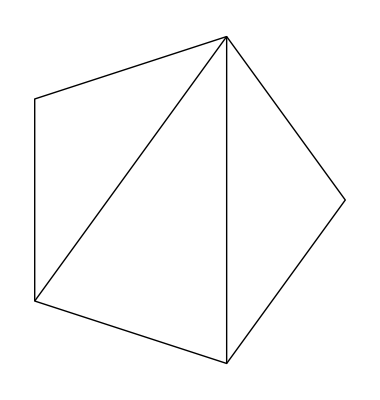
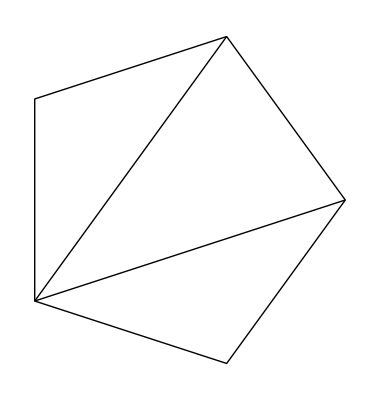
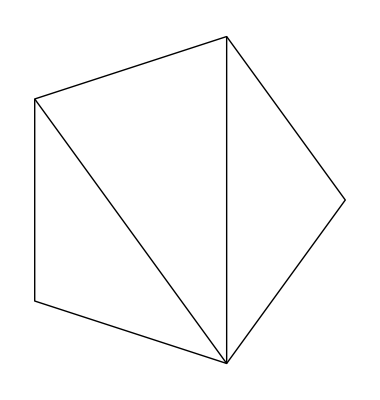
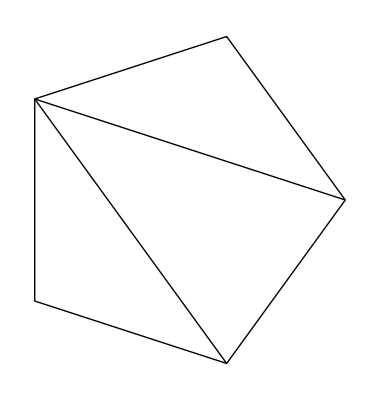
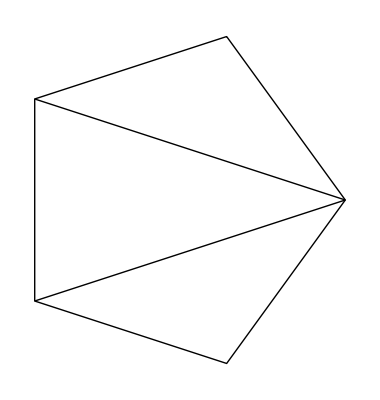

```mathematica
Table[Graphics[{Line/@Map[pts[[#]]&,lines[[n]]],Line[Append[pts,pts[[1]]]]}],{n,1,Length[lines]}]
```